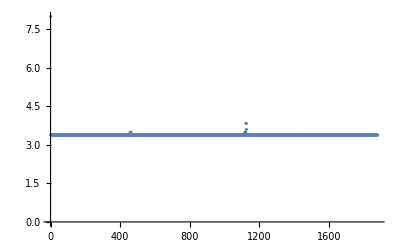

```mathematica
noteDir = NotebookDirectory[];
fileName = "229 RECT NO CAP 5.txt";
fullName = StringJoin[{noteDir, fileName}];

data = Import[fullName, "Data"];

data = Table[i[[1]], {i, data}];
ListPlot[data]
```